```mathematica
g = {{-f,0,0,0},{0,f,0,0},{0,0,r^2,0},{0,0,0,r^2 Sin[θ]^2}};
```

```mathematica
MatrixForm[g]
```

(gtt | 0 | 0 | 0
0 | grr | 0 | 0
0 | 0 | goo | 0
0 | 0 | 0 | gff)

```mathematica
g
```

{{gtt,0,0,0},{0,grr,0,0},{0,0,goo,0},{0,0,0,gff}}

```mathematica
Inverse[g]
```

{{1/gtt,0,0,0},{0,1/grr,0,0},{0,0,1/goo,0},{0,0,0,1/gff}}

```mathematica
DSolve[R''[r] - ((L (L+1))/r^2-ω^2-m^2)R[r]==0,R[r],r]
```

{{R[r]→√r BesselJ[1/2 (1+2 L),-ⅈ r √(-m^2-ω^2)] C[1]+√r BesselY[1/2 (1+2 L),-ⅈ r √(-m^2-ω^2)] C[2]}}

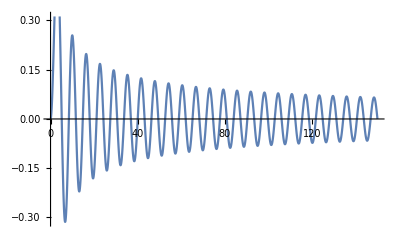

```mathematica
Plot[ BesselJ[2,x],{x,0,150}]
```

```mathematica
Clear[y]
```

```mathematica
DSolve[y''[x]+y[x] == (A Cos[x]+B Sin[x])^2,y[x],x]
```

{{y[x]→C[1] Cos[x]+C[2] Sin[x]+1/12 (3 A^2 Cos[x]^2+9 B^2 Cos[x]^2+A^2 Cos[x] Cos[3 x]-B^2 Cos[x] Cos[3 x]-6 A B Cos[x] Sin[x]-2 A B Cos[3 x] Sin[x]+10 A^2 Sin[x]^2+2 B^2 Sin[x]^2+2 A^2 Cos[2 x] Sin[x]^2-2 B^2 Cos[2 x] Sin[x]^2-8 A B Cos[x] Sin[x]^3)}}

```mathematica
f= 1 - 2/r;
```

```mathematica
Clear[R,f]
```

```mathematica
R[r]
```

R[r]

```mathematica
DSolve[R''[r]+2 f/r R'[r]-1/f (-ω^2/f + 2/r^3 + (L (L+1))/r^2-m^2) R[r]==0,R[r],r]
```

{{R[r]→DifferentialRoot[Function[{y,x},{(4-2 x+2 x L-x^2 L+2 x L^2-x^2 L^2-2 x^3 m^2+x^4 m^2+x^4 ω^2) y[x]+2 (-2+x)^3 y'[x]+(-2+x)^2 x^2 y''[x]==0,y[1]==C[1],y'[1]==C[2]}]][r]}}

```mathematica
R[r_]:=DifferentialRoot[Function[{y,x},{(4-2 x+2 x L-x^2 L+2 x L^2-x^2 L^2-2 x^3 m^2+x^4 m^2+x^4 ω^2) y[x]+2 (-2+x)^3 y'[x]+(-2+x)^2 x^2 y''[x]==0,y[1]==C[1],y'[1]==C[2]}]][r]
```